```mathematica
ab[x_]:= Piecewise[{{Abs[x],Abs[x]≤ Pi}}]
```

```mathematica
periodicExtension[func_,nPeriods_] = Sum[func[x+2k*Pi],{k,-nPeriods,nPeriods}]
```

∑_(k=-nPeriods)^nPeriods func[2 k π+x]

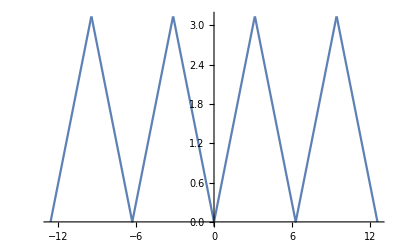

```mathematica
Plot[periodicExtension[ab,4],{x,-4Pi,4Pi},PlotRange->All]
```